```mathematica
Mark6 Disk Performance Results
```

## Introduction

This document describes the individual disk performance results for disks in Mark6 disk packs mk6 + 005, mk6 + 006, mk6 + 007, mk6 + 008, mk6 + 009. The results were measured using the FIO linux benchmarking program.

## External Libraries

```mathematica
Needs["ComputerArithmetic`"];
Needs["PlotLegends`"];
```

## Import Data

```mathematica
SetDirectory["/opt/src/mark6/tests/disk"];
nrDirectories={"mk6+005","mk6+006","mk6+007","mk6+008"};
(* mk6006, mk6007, mk6008 *)
nrFiles=FileNames[#<>"/disk*.log"]&/@nrDirectories

windowSize=120;
rawData=Function[files,
Function[file,
data=Import[file,"CSV"][[All,{1,2}]];
time=data[[All,1]]/1000;
averageData=MovingAverage[8/1000 data[[All,2]],windowSize];
Partition[Riffle[time,averageData],2]
]/@files
]/@nrFiles;

mk6005Data=rawData[[1]];
Length[mk6005Data]

mk6006Data=rawData[[2]];
Length[mk6006Data]

mk6007Data=rawData[[3]];
Length[mk6007Data]

mk6008Data=rawData[[4]];
Length[mk6008Data]
```

{{mk6+005/disk10_write_bw.log,mk6+005/disk11_write_bw.log,mk6+005/disk12_write_bw.log,mk6+005/disk13_write_bw.log,mk6+005/disk14_write_bw.log,mk6+005/disk15_write_bw.log,mk6+005/disk8_write_bw.log,mk6+005/disk9_write_bw.log},{mk6+006/disk0_write_bw.log,mk6+006/disk1_write_bw.log,mk6+006/disk2_write_bw.log,mk6+006/disk3_write_bw.log,mk6+006/disk4_write_bw.log,mk6+006/disk5_write_bw.log,mk6+006/disk6_write_bw.log,mk6+006/disk7_write_bw.log},{mk6+007/disk0_write_bw.log,mk6+007/disk1_write_bw.log,mk6+007/disk2_write_bw.log,mk6+007/disk3_write_bw.log,mk6+007/disk4_write_bw.log,mk6+007/disk5_write_bw.log,mk6+007/disk6_write_bw.log,mk6+007/disk7_write_bw.log},{mk6+008/disk0_write_bw.log,mk6+008/disk1_write_bw.log,mk6+008/disk2_write_bw.log,mk6+008/disk3_write_bw.log,mk6+008/disk4_write_bw.log,mk6+008/disk5_write_bw.log,mk6+008/disk6_write_bw.log,mk6+008/disk7_write_bw.log}}

8

8

8

«1 more identical outputs»

```mathematica
mk6007Serials={
"WD-WCATR5882337",
"WD-WCATR5842519",
"WD-WCATR5842024",
"WD-WCATR5854063",
"WD-WCATR5842518",
"WD-WCATR5873146",
"WD-WCATR5854139",
"WD-WCATR5873160"
};

mk6008Serials={
"WD-WCATR5862117",
	"WD-WCATR5836481",
	"WD-WCATR5861698",
	"WD-WCATR5841686",
	"WD-WCATR5861912",
	"WD-WCATR5882097",
	"WD-WCATR5879679",
	"WD-WCATR5879319"
};

mk6005Serials={
	"WD-WCATR5882572",
	"WD-WCATR5862262",
	"WD-WCATR5861552",
	"WD-WCATR5879674",
	"WD-WCATR5873892",
	"WD-WCATR5861375",
	"WD-WCATR5879596",
	"WD-WCATR5884830"
};

mk6006Serials={
"WD-WCATR5861771",
"WD-WCATR5862741",
"WD-WCATR5880404",
"WD-WCATR5880028",
"WD-WCATR5870986",
"WD-WCATR5882830",
"WD-WCATR5880218",
"WD-WCATR5870859"
};
mk6009Serials={
"WD-WMAY01837808",
"WD-WMAY02074904",
"WD-WMAY02074917",
"WD-WMAY01790329",
"WD-WMAY02074892",
"WD-WMAY01548353",
"WD-WMAY02041851",
"WD-WMAY01299169"
};
```

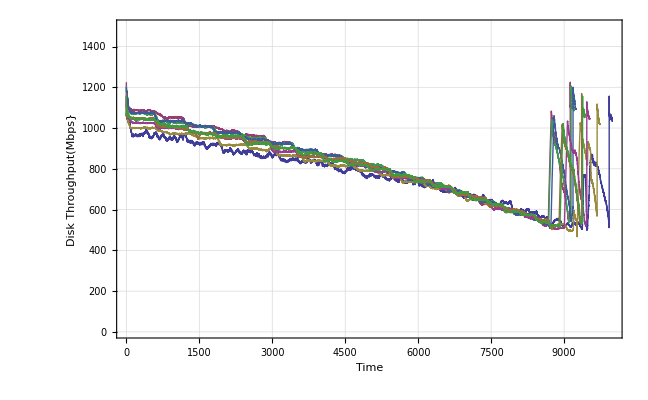

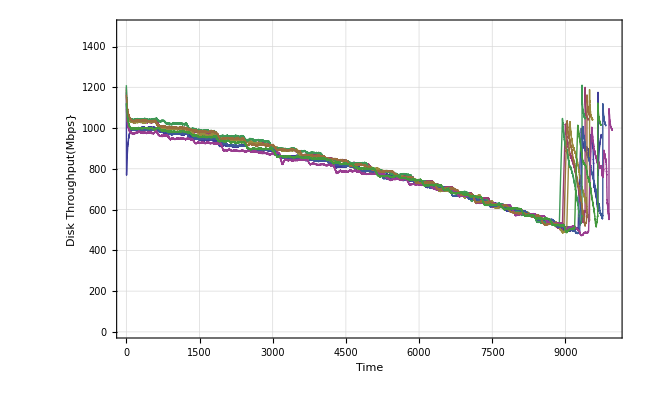

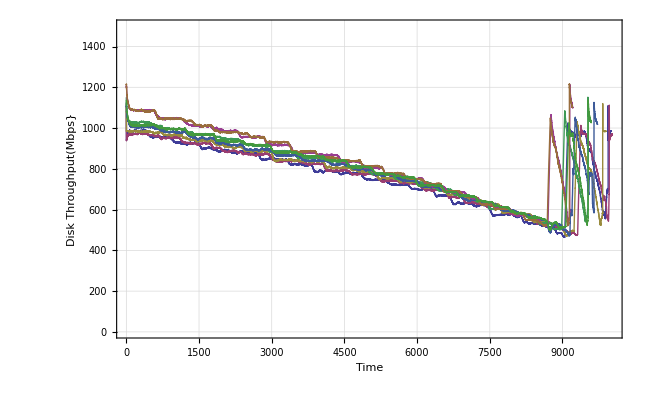

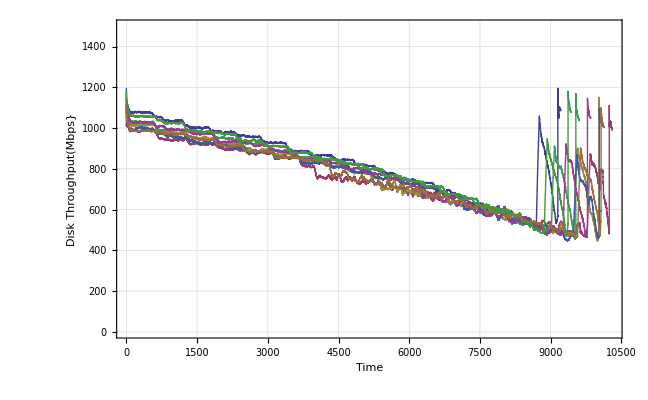

```mathematica
ListPlot[mk6005Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6005Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6006Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6006Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6007Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6007Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6008Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6008Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
```